# INTSECA

This notebook contains details of using twisted intersection theory to generate the master integrals and the associated canonical system for the single massive exchange diagram in FRW cosmology.

```mathematica
SetDirectory[NotebookDirectory[]];
<<INTSECA.wl
```

INTSECA 1.2.3

## single massive exchange (dS)

### Definitions

```mathematica
dim=4;
nkin=3;
kin={X1,X2,Y};
```

Untwisted hyperplanes:

```mathematica
nBplane=4;
B[1]={1,0,Y,0,X1+Y};
B[2]={0,1,0,Y,X2+Y};
B[3]={1,1,Y,-Y,X1+X2};
B[4]={1,1,-Y,Y,X1+X2};
```

Twisted hyperplanes:

```mathematica
nTplane=6;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,1,0,2};
T[5]={0,0,0,1,0};
T[6]={0,0,0,1,2};
powers={-e,-e,e,e,e,e};
twists={e};
```

two twists, one for mass and the other for FRW

Wavefunction:

let’s deal with the inhomogeneous part: (anti-)time-ordered

```mathematica
psi=⟨1,3,5,6⟩-⟨2,4,5,6⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

116

```mathematica
sol=Sol[];
```

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({3} | {⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩}
{4} | {⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}
{1,2} | {⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩}
{1,3} | {⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩}
{1,4} | {⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩}
{2,3} | {⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩}
{2,4} | {⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩}
{3,4} | {⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩}
{1,2,3} | {⟨1,2,3,5⟩,⟨1,2,3,7⟩}
{1,2,4} | {⟨1,2,4,6⟩,⟨1,2,4,9⟩}
{1,3,4} | {⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩}
{2,3,4} | {⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩}
{1,2,3,4} | {⟨1,2,3,4⟩})

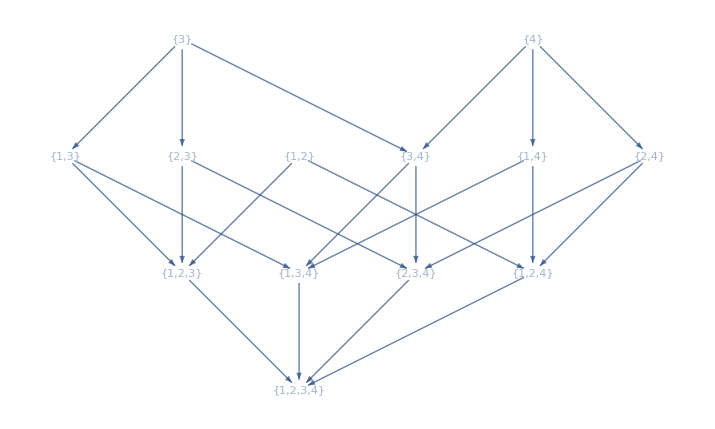

# codimension | 0 | 1 | 2 | 3 | 4
# boundaries | 0 | 2 | 6 | 4 | 1

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

```mathematica
basis=bdyBasis[[2]]//Flatten;
```

```mathematica
basis//Length
```

50

```mathematica
EchoTiming[A0 = AMatrix[0]];
A0[[1]] // MatrixPlot
```

11.3547

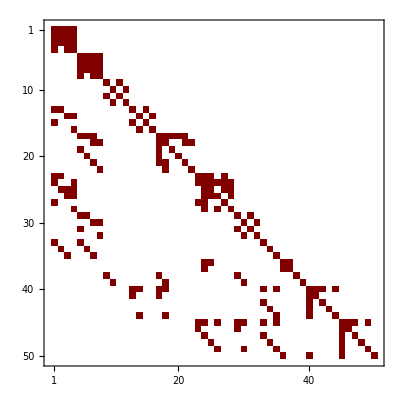

### Basis reduction: filtering

#### start

The stored A-matrix from previous overcomplete set of basis functions:

ClearAll[basis, A0, A];
Get[FileNameJoin[{NotebookDirectory[], "storage", "basis_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A0_single-massive-exchange"}]];

basis // Length
A0[[1]] // Length
A[[1]] // Length

50

50

44

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(e (Log[X1+X2]-3 Log[Y]) | e (-Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-3 Log[Y]) | e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (Log[Y]-Log[X1+X2+2 Y]) | e (Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X1+Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-2 Log[Y]+Log[X1+Y]-Log[X2+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (-2 Log[Y]-Log[X1+Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+Y]+Log[X2+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[-2 X1-X2-Y]+Log[2 X1+X2-Y]) | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[Y]) | e (-Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | 0 | e (Log[X2-3 Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | e (Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y]) | e (Log[X2-3 Y]-Log[Y]) | e (Log[X2-3 Y]-Log[X2-Y]) | e (-Log[X2-3 Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y]) | 0 | e (Log[X2+Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[X2+3 Y]) | e (Log[X2-Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[Y]) | e (Log[-2 X1-X2-Y]-Log[X2+3 Y]) | e (-Log[X2-Y]+Log[Y]) | e (Log[Y]-Log[X2+3 Y]) | e (-Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y]) | e (-Log[X2-Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2-Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2-Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1+2 X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (-Log[Y]+Log[X1+3 Y]) | e (-Log[X1-Y]+Log[X1+3 Y]) | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1+2 X2-Y]-Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y]) | 0 | e (-Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-3 Y]+Log[X2+Y]) | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[Y]) | e (-Log[X1-3 Y]+Log[Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X2-Y]-Log[X1+2 X2+Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | e (-2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (-Log[X2-Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-4 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (-Log[X1-Y]-2 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | 0 | e Log[Y] | e (Log[X1+X2]-Log[Y]) | 0 | 0 | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e Log[X1+X2] | -e Log[Y] | e Log[Y] | 0 | e Log[X1+X2] | e Log[Y] | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[Y] | e (-2 Log[X1+X2]-2 Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1+X2]+Log[Y]) | -e Log[Y] | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[Y] | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]-2 Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]-2 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | e (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y]) | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | e (-Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | -e Log[Y] | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | 0 | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2+Y] | e Log[Y] | -e Log[X2+Y] | -e Log[Y] | 0 | -e Log[Y] | 0 | -e Log[X2+Y] | -e Log[Y] | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | e Log[X1-Y] | e Log[X2+Y] | -e Log[Y] | e (-Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | e Log[Y] | 0 | e (Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e Log[Y] | 0 | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y]) | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | e (-Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | -e Log[Y] | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e Log[Y] | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0 | e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2-Y] | 0 | e Log[X1+Y] | e Log[Y] | -e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | e Log[Y] | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+Y] | e Log[X2-Y] | -e Log[Y] | e (-Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | -e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | e Log[Y] | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | -e Log[Y] | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e Log[Y] | 0 | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | e (-Log[X2]+Log[Y]) | 0 | e (Log[X1]-Log[Y]) | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (-Log[X1]-Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{X1,X2,X1+X2,X1-3 Y,X2-3 Y,X1+X2-2 Y,X1-Y,-2 X1-X2-Y,X2-Y,2 X1+X2-Y,X1+2 X2-Y,Y,X1+Y,X2+Y,X1+2 X2+Y,X1+X2+2 Y,X1+3 Y,X2+3 Y}

18

```mathematica
Coefficient[Amatrix,e]//MatrixForm
```

(Log[X1+X2]-3 Log[Y] | -Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2]-Log[Y] | Log[X1+X2-2 Y]-3 Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | -Log[X1+X2-2 Y]+Log[Y] | Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y] | -2 Log[X1+X2]+2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-3 Log[Y] | Log[X1+X2-2 Y]-Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | -3 Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | Log[Y]-Log[X1+X2+2 Y] | Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y] | -2 Log[X1+X2]+2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X1+Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -2 Log[Y]+Log[X1+Y]-Log[X2+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | -2 Log[Y]-Log[X1+Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[Y]-Log[X2+Y] | -Log[X1+Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+Y]-Log[X2+Y] | Log[X1-Y]-Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-Y]+Log[X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+Y]+Log[X2+Y] | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | Log[X2-Y]-2 Log[Y]-Log[X1+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[-2 X1-X2-Y]+Log[2 X1+X2-Y] | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-2 X1-X2-Y]-Log[Y] | -Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | 0 | Log[X2-3 Y]-Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y] | Log[X2-3 Y]-Log[Y] | Log[X2-3 Y]-Log[X2-Y] | -Log[X2-3 Y]+Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | Log[X2+Y]-Log[X2+3 Y] | -Log[X2+Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | -Log[X2+Y]+Log[X2+3 Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y] | 0 | Log[X2+Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[X2+3 Y] | Log[X2-Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[Y] | Log[-2 X1-X2-Y]-Log[X2+3 Y] | -Log[X2-Y]+Log[Y] | Log[Y]-Log[X2+3 Y] | -Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y] | -Log[X2-Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X2-Y]+Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2-Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2-Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1+2 X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+2 X2+Y]-Log[X1+3 Y] | 0 | 0 | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y] | -Log[Y]+Log[X1+3 Y] | -Log[X1-Y]+Log[X1+3 Y] | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Log[X1+2 X2-Y]-Log[X1+Y] | Log[X1-3 Y]-Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y] | 0 | -Log[X1+2 X2-Y]+Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-3 Y]+Log[X2+Y] | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1-Y]+Log[Y] | -Log[X1-3 Y]+Log[Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X2-Y]-Log[X1+2 X2+Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | -2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | -Log[X2-Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-4 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2-Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[X1-Y]-2 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | 0 | Log[Y] | Log[X1+X2]-Log[Y] | 0 | 0 | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2]-Log[Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[X1+X2] | -Log[Y] | Log[Y] | 0 | Log[X1+X2] | Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y] | -2 Log[X1+X2]-2 Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1+X2]+Log[Y] | -Log[Y] | 0 | 0 | Log[X1+X2]-Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y] | 0 | -2 Log[X1+X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | -Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]-2 Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[X2-Y] | 0 | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]-2 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y] | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | -Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | 0 | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2+Y] | Log[Y] | -Log[X2+Y] | -Log[Y] | 0 | -Log[Y] | 0 | -Log[X2+Y] | -Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | Log[X1-Y] | Log[X2+Y] | -Log[Y] | -Log[X1-Y]-2 Log[Y]-Log[X2+Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | Log[Y] | 0 | Log[Y]-Log[X1+Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | Log[Y] | 0 | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y] | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2-Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | -Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | Log[Y] | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0 | Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y] | 0 | Log[X1+Y] | Log[Y] | -Log[X2-Y] | -Log[Y] | Log[X2-Y] | -Log[Y] | Log[X2-Y] | Log[Y] | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+Y] | Log[X2-Y] | -Log[Y] | -Log[X2-Y]-2 Log[Y]-Log[X1+Y] | -Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | Log[Y] | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[Y] | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | Log[Y] | 0 | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | -Log[X2]+Log[Y] | 0 | Log[X1]-Log[Y] | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X1]+Log[Y] | -Log[X2]+Log[Y] | 0 | 0 | 0 | -Log[X1]-Log[X2])

we can pick

```mathematica
need=Position[basis,#]&/@(Join[
{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩},
{⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩},
{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩},
{⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}])//Flatten
```

{13,14,15,16,29,30,31,32,1,2,3,4,5,6,7,8}

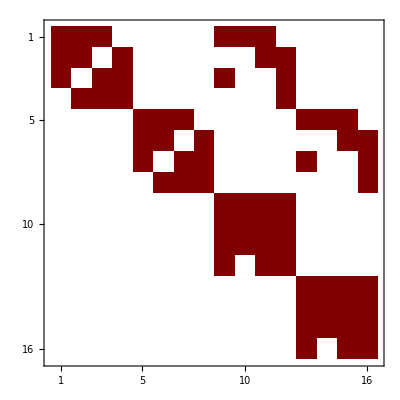

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->Coefficient[AmatrixNeed,e].basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y],Log[Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩,-4 ⟨1,3,5,6⟩+4 ⟨2,4,5,6⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | -⟨3,5,6,7⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,7⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | ⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩)

{⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

5

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

20

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,False,False,True,False,True,True,True,False,True,False,False,True,True,True,True,False,False,True,False}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

6

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

{{{2},{17}}}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

14

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

6

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

8

6 = 1 + (2+1) + (1+1)
8 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_13
φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15
φ_1+φ_3+φ_7+φ_9-φ_14
φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16
φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_5

so psi is just the new basis 1.

### A matrix (associated to physical basis)

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basisNeed[[j]]],{i,1,Length[Basis]},{j,1,Length[basisNeed]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Amatrix6=Umatrix.AmatrixNeed.Uinv//Simplify;
%//MatrixForm
```

(2 e (-2 Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0
e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]+Log[X2-Y]-Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y])
e (Log[X1+X2-2 Y]-Log[X1-Y]-2 Log[Y]+2 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1-Y]+Log[X1+Y])
e (Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | 0 | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2]-Log[X2-Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X2-Y]-Log[X2+Y])
-e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | 0 | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | -e (Log[X1+X2-2 Y]+Log[X1+X2+2 Y]) | 0
e (-Log[X1-Y]+Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]) | e (Log[X1-Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | -e (Log[X1-Y]+Log[X2+Y]))

{1,2,3} {4,5} {6,7,8}
notice that l7, l8 are suspicious poles. To eliminate the spurious poles, we may further reduce the size. (there is further redundancy in the integral repr. of Hankel function)
6 = 1 + (2+1) + (1+1)

```mathematica
lett=Join[l0,Complement[l1,l0],Complement[l2,l1]]
```

{Log[X1+Y],Log[X2+Y],Log[Y],Log[X1-Y],Log[X2-Y],Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

the matrix is not upper triangular...

```mathematica
A6=Coefficient[Amatrix6,e]/. Thread[lett->Table[ToExpression["L"<>ToString[i]],{i,1,Length[letters]}]]//Simplify
```

{{2 (L2-2 L3),-L2+L4,-L2+L5,L1-L2,0,0},{L2-L7,-3 L3+L7,-L2+L5,L1-L2-L3+L7,-L2+L5+L6-L7,L2-L5},{2 L2-2 L3-L4+L7,-L2+L3+L4-L7,-L2-2 L3+L4,-L2+L3+L4-L7,-L6+L7,L1-L4},{L2-L8,-L2-L3+L4+L8,0,-3 L3+L8,L2-L5+L6-L8,-L2+L5},{2 L3-L7-L8,-2 L3+L7+L8,0,-2 L3+L7+L8,-L7-L8,0},{L2+L3-L4-L8,-L2-L3+L4+L8,-L3+L4,-2 L3+L4+L8,L2-L8,-L2-L4}}

```mathematica
%//MatrixForm
```

(2 (L2-2 L3) | -L2+L4 | -L2+L5 | L1-L2 | 0 | 0
L2-L7 | -3 L3+L7 | -L2+L5 | L1-L2-L3+L7 | -L2+L5+L6-L7 | L2-L5
2 L2-2 L3-L4+L7 | -L2+L3+L4-L7 | -L2-2 L3+L4 | -L2+L3+L4-L7 | -L6+L7 | L1-L4
L2-L8 | -L2-L3+L4+L8 | 0 | -3 L3+L8 | L2-L5+L6-L8 | -L2+L5
2 L3-L7-L8 | -2 L3+L7+L8 | 0 | -2 L3+L7+L8 | -L7-L8 | 0
L2+L3-L4-L8 | -L2-L3+L4+L8 | -L3+L4 | -2 L3+L4+L8 | L2-L8 | -L2-L4)

#### check flatness

```mathematica
Amatrix6//MatrixForm
```

(2 e (-2 Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0
e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]+Log[X2-Y]-Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y])
e (Log[X1+X2-2 Y]-Log[X1-Y]-2 Log[Y]+2 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1-Y]+Log[X1+Y])
e (Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | 0 | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2]-Log[X2-Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X2-Y]-Log[X2+Y])
-e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | 0 | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | -e (Log[X1+X2-2 Y]+Log[X1+X2+2 Y]) | 0
e (-Log[X1-Y]+Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]) | e (Log[X1-Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | -e (Log[X1-Y]+Log[X2+Y]))

```mathematica
Amatrix6;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

#### DEQ

can we directly derive the PDE with the above 6x6 A-matrix?

we need to also convert the ODE to PDE.

### Impose symmetry from integral

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨3,5,6,7⟩->⟨4,5,6,9⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩}/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{φ_16→-φ_12,φ_9→φ_15,φ_13→φ_11,φ_14→-φ_10-φ_11-φ_15}

```mathematica
BasisIndex
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_13,φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15,φ_1+φ_3+φ_7+φ_9-φ_14,φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16,φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16}

```mathematica
BasisIndex//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_13
φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15
φ_1+φ_3+φ_7+φ_9-φ_14
φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16
φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16)

```mathematica
BasisSym=BasisIndex/.symForBasis;
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_11
φ_1-φ_2-φ_6-φ_10+φ_11
φ_1+φ_3+φ_7+φ_10+φ_11+2 φ_15
-2 φ_11+4 φ_12+2 φ_15
φ_1-φ_2+φ_3+φ_4-φ_8+2 φ_12+2 φ_15)

```mathematica
lett
```

{Log[X1+Y],Log[X2+Y],Log[Y],Log[X1-Y],Log[X2-Y],Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Table[Coefficient[BasisSym[[i]],Subscript[φ,j]],{i,1,6},{j,1,16}];
%//MatrixRank
```

6

```mathematica
A6//MatrixForm
```

(2 (L2-2 L3) | -L2+L4 | -L2+L5 | L1-L2 | 0 | 0
L2-L7 | -3 L3+L7 | -L2+L5 | L1-L2-L3+L7 | -L2+L5+L6-L7 | L2-L5
2 L2-2 L3-L4+L7 | -L2+L3+L4-L7 | -L2-2 L3+L4 | -L2+L3+L4-L7 | -L6+L7 | L1-L4
L2-L8 | -L2-L3+L4+L8 | 0 | -3 L3+L8 | L2-L5+L6-L8 | -L2+L5
2 L3-L7-L8 | -2 L3+L7+L8 | 0 | -2 L3+L7+L8 | -L7-L8 | 0
L2+L3-L4-L8 | -L2-L3+L4+L8 | -L3+L4 | -2 L3+L4+L8 | L2-L8 | -L2-L4)

```mathematica
{{1,1,0},{1,0,1},{a,b,c}}//Det
```

a-b-c

```mathematica
{{1,0,0,0},{-1,1,1,0},{-1,1,0,1},{2,-1,-1,-1}}//Det
```

1

```mathematica
{{1,0,0,0},{-1,1,1,0},{-1,1,0,1},{2,-1,-1,-1}}//Inverse
```

{{1,0,0,0},{0,1,1,1},{1,0,-1,-1},{1,-1,0,-1}}

```mathematica
BasisIndex[[{2,3,4}]]//Total
```

2 φ_1-φ_2-φ_5-φ_6+φ_9+φ_10+φ_11+φ_15

#### Basis transformation

```mathematica
U={{1,0,0,0,0,0},{-1,1,1,0,0,0},{-1,1,0,1,0,0},{2,-1,-1,-1,0,0},
{1,0,-1,-1,0,1},{-1,1,0,1,-1,0}};
%//Det
```

1

```mathematica
Uinv={{1,0,0,0,0,0},{-1,1,1,0,0,0},{-1,1,0,1,0,0},{2,-1,-1,-1,0,0},
{1,0,-1,-1,0,1},{-1,1,0,1,-1,0}}//Inverse
```

{{1,0,0,0,0,0},{0,1,1,1,0,0},{1,0,-1,-1,0,0},{1,-1,0,-1,0,0},{0,0,1,0,0,-1},{1,-1,-1,-2,1,0}}

```mathematica
U.Table[Subscript[a, i],{i,1,6}]
```

{a_1,-a_1+a_2+a_3,-a_1+a_2+a_4,2 a_1-a_2-a_3-a_4,a_1-a_3-a_4+a_6,-a_1+a_2+a_4-a_5}

```mathematica
B6=U.A6.Uinv//Simplify;
%//MatrixForm
```

(L1-4 L3+L5 | -L1+L4 | L4-L5 | -L1+L2+L4-L5 | 0 | 0
L1-L5 | -L1-2 L3+L5 | -L1-L2+2 L5 | -2 L1+2 L5 | L1+L2-L4-L5 | L2-L5
0 | 0 | -4 L3+2 L6 | 0 | 0 | -2 L6+L7+L8
-L3+L5 | 0 | L1+L3-L5-L6 | L1-2 L3-L5 | -L1+L4 | L6-L8
0 | -L3+L5 | L1-2 L3+L5 | L1-2 L3+L5 | -L1-L5 | -L5+L7
0 | 0 | -2 L3+2 L6 | 0 | 0 | -2 L6)

indeed, L7 and L8 only appear for J6.

#### dJ_2

```mathematica
-A6[[1]]+A6[[2]]+A6[[3]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{L2+2 L3-L4,-2 L3,-L2-2 L3+L4,-L2+L4,-L2+L5,L1+L2-L4-L5}

(L2+2 L3-L4) x_1-2 L3 x_2+(-L2-2 L3+L4) x_3+(-L2+L4) x_4+(-L2+L5) x_5+(L1+L2-L4-L5) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(x_6
x_1-x_3-x_4-x_5+x_6
2 x_1-2 x_2-2 x_3
-x_1+x_3+x_4-x_6
x_5-x_6
0
0
0)

#### dJ_3

```mathematica
-A6[[1]]+A6[[2]]+A6[[4]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{4 L3-L7-L8,-4 L3+L7+L8,0,-4 L3+L7+L8,2 L6-L7-L8,0}

(4 L3-L7-L8) x_1+(-4 L3+L7+L8) x_2+(-4 L3+L7+L8) x_4+(2 L6-L7-L8) x_5

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
0
4 x_1-4 x_2-4 x_4
0
0
2 x_5
-x_1+x_2+x_4-x_5
-x_1+x_2+x_4-x_5)

#### dJ_4

```mathematica
2A6[[1]]-A6[[2]]-A6[[3]]-A6[[4]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{-6 L3+L4+L8,3 L3-L8,2 L3-L4+L5,L1+3 L3-L4-L8,-L6+L8,-L1+L4}

(-6 L3+L4+L8) x_1+(3 L3-L8) x_2+(2 L3-L4+L5) x_3+(L1+3 L3-L4-L8) x_4+(-L6+L8) x_5+(-L1+L4) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(x_4-x_6
0
-6 x_1+3 x_2+2 x_3+3 x_4
x_1-x_3-x_4+x_6
x_3
-x_5
0
x_1-x_2-x_4+x_5)

```mathematica
BasisIndex[[1]]-BasisIndex[[2]]-BasisIndex[[4]]+BasisIndex[[5]]//Simplify
```

-φ_10-φ_11+2 φ_12+φ_14+φ_15-2 φ_16

#### dI_5

```mathematica
A6[[5]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{2 L3-L7-L8,-2 L3+L7+L8,0,-2 L3+L7+L8,-L7-L8,0}

(2 L3-L7-L8) x_1+(-2 L3+L7+L8) x_2+(-2 L3+L7+L8) x_4-(L7+L8) x_5

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
0
2 x_1-2 x_2-2 x_4
0
0
0
-x_1+x_2+x_4-x_5
-x_1+x_2+x_4-x_5)

#### dI_6

```mathematica
A6[[6]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{L2+L3-L4-L8,-L2-L3+L4+L8,-L3+L4,-2 L3+L4+L8,L2-L8,-L2-L4}

(L2+L3-L4-L8) x_1+(-L2-L3+L4+L8) x_2+(-L3+L4) x_3+(-2 L3+L4+L8) x_4+(L2-L8) x_5-(L2+L4) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
x_1-x_2+x_5-x_6
x_1-x_2-x_3-2 x_4
-x_1+x_2+x_3+x_4-x_6
0
0
0
-x_1+x_2+x_4-x_5)